### plot style

```mathematica
SetOptions[{Plot, ListPlot, ListLinePlot, ListLogPlot, ListLogLogPlot}, {BaseStyle -> {FontFamily -> "Times", FontSize -> 18}, PlotStyle -> ColorData[108, "ColorList"], PlotRange -> All, Frame -> True, FrameLabel -> {"R (a_0)", "E (GHz × h)"}, GridLines -> Automatic, PlotLegends -> "Expressions", ImageSize -> Medium}];
```

## quantum reflection states of ULRM at n = 30

## Setup

### Atomic Units Conversion

#### Boltzmann constant [T/J]

```mathematica
kB = 1.380649*10^(-23);
```

#### Bohr unit of length [m]

```mathematica
a0 = 5.29177210903*10^(-11);
```

#### time [s]

```mathematica
ts = 2.4188843265857*10^(-17);
```

#### velocity [m/s]

```mathematica
vms = 2.18769126364*10^6; (* =a0/ts *)
```

#### electron mass [kg]

```mathematica
me = 9.1093837015*10^(-31);
```

#### atomic mass in units of electron mass

```mathematica
M = 86.909180527*1822.888486192;(* atomic mass *)
```

#### temperatures from nK to K

```mathematica
T = Table[10^t, {t,-9,0,1}];
```

#### corresponding velocities in atomic units

```mathematica
vs = Sqrt[3 kB T/(M me)]/vms;
```

### Wavefunctions

#### Energies are displayed GHz

```mathematica
unit = 2 3.289841960355 10^6;
```

#### Radial hydrogenic wave function

```mathematica
U[n_,l_,r_] := Sqrt[(2/n)^3 ((n-l-1)!/(2n(n+l)!))] Exp[-r/n] (2(r/n))^l LaguerreL[n-l-1,2l+1,2(r/n)]
dU[n_,l_,r_] := D[x U[n,l,x],x] /. x->r
```

#### Radial quantum defect state wave function

```mathematica
W[n_,l_,r_] := 1/n/Sqrt[(n+l)! (n-l-1)!] WhittakerW[n,l+1/2,2r/n]/r
dW[n_,l_,r_] := D[x W[n,l,x],x] /. x->r
```

#### Angular wave function

```mathematica
Y[l_] := Sqrt[(2l+1)/(4π)]
```

#### Quantum defects for Rubidium

```mathematica
δRb = {3.1311804,2.65,1.34,0.0165192};
δ[l_]=If[l<Length[δRb],δRb[[l+1]],0];
```

#### Semi-classical electron wave number

```mathematica
kin[r_, n_] = Sqrt[2(-(2n^2)^(-1) + 1/r)];
```

#### Energy dependent scattering length (finite range theory)

```mathematica
A[k_] = -16.1+π/3 319.2Re[k];
```

#### Matrix element for the f state

```mathematica
Fstate[n_, r_] := W[n-δ[3],3,r] Y[3]
```

#### F-state energy offset

```mathematica
Fenergy[n_] := 1/2/n^2-1/2/(n-δ[3])^2
```

#### Matrix element for the trilobite

Alternative formulation for fractional n

```mathematica
TrilU[n_, r_] := Sqrt[(r(2n^2-r)(U[n,0,r]/n)^2+dU[n,0,r]^2)/(4π)]
TrilW[n_, r_] := Sqrt[(r(2n^2-r)(W[n,0,r]/n)^2+dW[n,0,r]^2)/(4π)]
Trilobite[n_, r_] := If[n∈Integers, TrilU[n,r], TrilW[n,r]]
```

However, for integer n, this is numerically more stable

```mathematica
Trilobite[n_, r_] := Sqrt[Sum[U[n,l,r]^2 Y[l]^2,{l,4,n-1}]]
```

## Electronic potentials

### Parameters

```mathematica
n0 = 30;
R = Subdivide[0.6n0^2,2.5n0^2,400];
```

### Two state model

#### Set up 2x2 Matrix

```mathematica
Hamiltonian[n_, r_] := With[{a=2π A[kin[r,n]], t=Trilobite[n,r], f=Fstate[n,r], e=Fenergy[n]}, {{a t^2, a t f}, {a t f, e+a f^2}}]
```

#### Diagonalization

```mathematica
Diabatic = Table[Hamiltonian[n0, r], {r,R}];
Adiabatic = Table[Eigenvalues[Diabatic[[i]]], {i,Length[Diabatic]}];
```

```mathematica
dt = Diabatic[[All,1,1]];
df = Diabatic[[All,2,2]];
do = Diabatic[[All,1,2]];
at = Adiabatic[[All,1]];
af = Adiabatic[[All,2]];
```

#### Diabatic Potentials

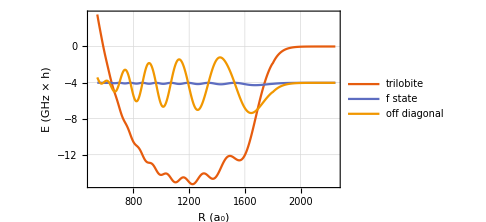

```mathematica
ListLinePlot[{{R, dt unit}ᵀ, {R, df unit}ᵀ, {R, 2 do unit+df unit}ᵀ}, PlotLegends->{"trilobite", "f state", "off diagonal"}]
```

#### Adiabatic Potentials

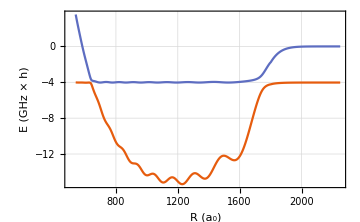

```mathematica
ListLinePlot[{{R, at unit}ᵀ, {R, af unit}ᵀ}]
```

### Exact diagonalization

#### Set of quantum numbers

```mathematica
nl = Flatten[Table[{n,l}, {n,{n0-1,n0}}, {l,0,n-1}],1];
```

#### Basis states

```mathematica
ρ[n_, l_, r_] := If[l<4, W[n-FractionalPart[δ[l]],l,r], U[n,l,r]]
```

```mathematica
B[r_] := Table[With[{n=nl[[i,1]], l=nl[[i,2]]}, N[ρ[n,l,r]]], {i,Length[nl]}]
Bθ = Table[With[{l=nl[[i,2]]}, N[Y[l]]], {i,Length[nl]}];
```

#### Import s - wave scattering data

```mathematica
(* As = Interpolation[Import["/home/fhummel/Documents/Wolfram Mathematica/fstates/data/Rbscat.csv", "Data"][[All,{1,2}]]]; *)
As = Interpolation[Import["/home/frederic/Documents/Wolfram Mathematica/data/Rbscat.csv", "Data"][[All,{1,2}]]];
```

#### Interaction potential

```mathematica
Vθ = Outer[Times, Bθ, Bθ];
V[r_] := 2π A[kin[r,n0]] With[{b = B[r]}, Outer[Times, b, b]] unit
VS[r_] := Vθ V[r]
```

#### Rydberg energies

```mathematica
N0 = Table[With[{n=nl[[i,1]], l=nl[[i,2]]}, N[n-FractionalPart[δ[l]]]], {i,Length[nl]}];
```

```mathematica
E0 = unit/2 (1/n0^2-1/N0^2);
```

#### Polarization potential

```mathematica
Pol[R_] := -319.2/(2R^4) unit
```

#### Diagonalization

```mathematica
Sol[r_] := Sort[Eigenvalues[DiagonalMatrix[E0]+VS[r]]]+Pol[r]
```

```mathematica
pes = ParallelTable[Sol[r], {r,R}]; // Timing
```

{1.8373,Null}

#### Trilobite / f state

This is equivalent to the two state model

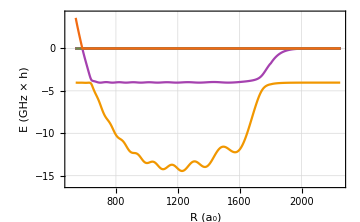

```mathematica
ListLinePlot[pesᵀ, PlotRange->{-16,4}, DataRange->{R[[1]],R[[-1]]}]
```

#### s state

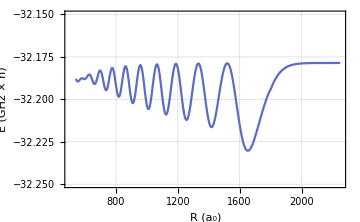

```mathematica
ListLinePlot[pesᵀ, PlotRange->{-32.25,-32.15}, DataRange->{R[[1]],R[[-1]]}]
```

#### d state

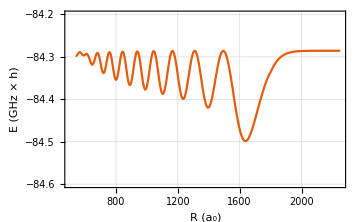

```mathematica
ListLinePlot[pesᵀ, PlotRange->{-84.6,-84.2}, DataRange->{R[[1]],R[[-1]]}]
```

#### p state

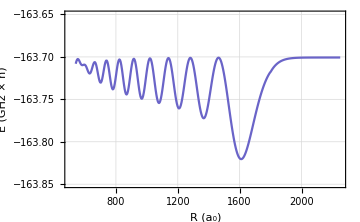

```mathematica
ListLinePlot[pesᵀ, PlotRange->{-163.85,-163.65}, DataRange->{R[[1]],R[[-1]]}]
```

### Exact diagonalization including p-wave interaction

#### Set of quantum numbers

```mathematica
nlm = Flatten[Table[{n,l}, {n,{n0-1,n0}}, {l,1,n-1}],1];
```

#### Basis states

```mathematica
Bpθ = Table[With[{l=nlm[[i,2]]}, N[D[SphericalHarmonicY[l,1,β,0],β]]], {i,Length[nlm]}] /. β->0;
```

```mathematica
Bp[r_] := Table[With[{n=nlm[[i,1]], l=nlm[[i,2]]}, N[ρ[n,l,r]]], {i,Length[nlm]}]
Bd[r_] := Table[With[{n=nl[[i,1]], l=nl[[i,2]]}, N[D[ρ[n,l,ξ],ξ]]], {i,Length[nl]}] /. ξ->r
```

#### Import p - wave scattering data

```mathematica
(* ApMod = Import["/home/fhummel/Documents/Wolfram Mathematica/fstates/data/Rbscat.csv", "Data"][[All,{1,3}]]; *)
ApMod = Import["/home/frederic/Documents/Wolfram Mathematica/data/Rbscat.csv", "Data"][[All,{1,3}]];
cut = 224;
ApMod[[1;;cut,2]] = Table[ApMod[[cut,2]], {i,cut}];
Ap = Interpolation[ApMod];
```

#### P-wave interaction potential

m = 0

```mathematica
Vd[r_] := 6π Ap[Re[kin[r,n0]]] With[{b = Bd[r]}, Outer[Times, b, b]] unit
VD[r_] := Vθ Vd[r]
```

m = 1

```mathematica
Vdθ = Outer[Times, Bpθ, Bpθ];
Vp[r_] := 6π Ap[Re[kin[r,n0]]] With[{b = Bp[r]}, Outer[Times, b, b]] unit
VP[r_] := 2 Vdθ Vp[r]/r^2
```

#### Rydberg energies

```mathematica
NP = Table[With[{n=nlm[[i,1]], l=nlm[[i,2]]}, N[n-FractionalPart[δ[l]]]], {i,Length[nlm]}];
```

```mathematica
EP = unit/2 (1/n0^2-1/NP^2);
```

#### Diagonalization

```mathematica
SolP0[r_] := Sort[Eigenvalues[DiagonalMatrix[E0]+VS[r]+VD[r]]]+Pol[r]
SolP1[r_] := Sort[Eigenvalues[DiagonalMatrix[EP]+VP[r]]]+Pol[r]
```

```mathematica
pesP0 = ParallelTable[SolP0[r], {r,R}]; // Timing
```

{2.05388,Null}

```mathematica
pesP1 = ParallelTable[SolP1[r], {r,R}]; // Timing
```

{0.414318,Null}

#### Overview

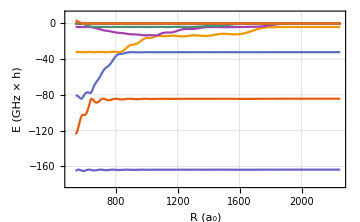

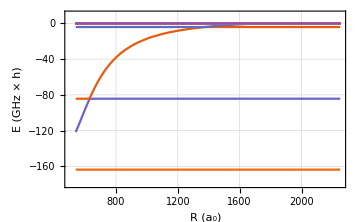

```mathematica
ListLinePlot[pesP0ᵀ, PlotRange->{-180,10}, DataRange->{R[[1]],R[[-1]]}]
ListLinePlot[pesP1ᵀ, PlotRange->{-180,10}, DataRange->{R[[1]],R[[-1]]}]
```

#### Trilobite / f state

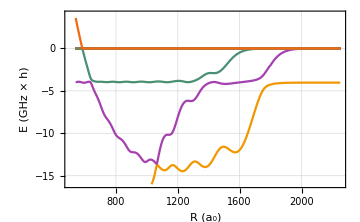

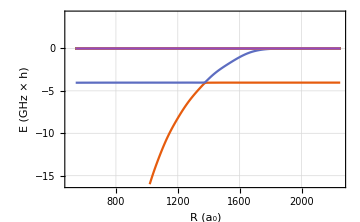

```mathematica
ListLinePlot[pesP0ᵀ, PlotRange->{-16,4}, DataRange->{R[[1]],R[[-1]]}]
ListLinePlot[pesP1ᵀ, PlotRange->{-16,4}, DataRange->{R[[1]],R[[-1]]}]
```

#### s state

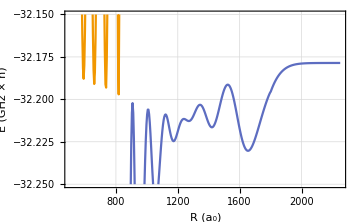

```mathematica
ListLinePlot[pesP0ᵀ, PlotRange->{-32.25,-32.15}, DataRange->{R[[1]],R[[-1]]}]
```

#### d state

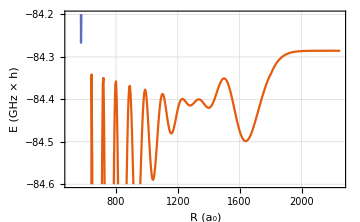

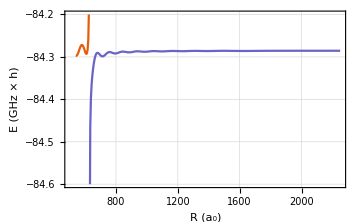

```mathematica
ListLinePlot[pesP0ᵀ, PlotRange->{-84.6,-84.2}, DataRange->{R[[1]],R[[-1]]}]
ListLinePlot[pesP1ᵀ, PlotRange->{-84.6,-84.2}, DataRange->{R[[1]],R[[-1]]}]
```

#### p state

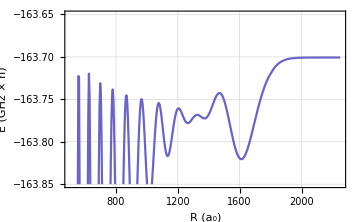

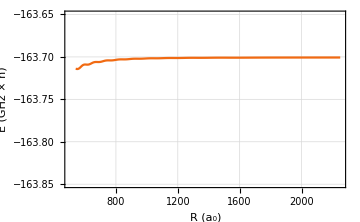

```mathematica
ListLinePlot[pesP0ᵀ, PlotRange->{-163.85,-163.65}, DataRange->{R[[1]],R[[-1]]}]
ListLinePlot[pesP1ᵀ, PlotRange->{-163.85,-163.65}, DataRange->{R[[1]],R[[-1]]}]
```

### Borodin-Kazansky model

#### phase shifts

```mathematica
δs[k_] := ArcTan[-k A[k]]
δp[k_] := With[{δ=ArcTan[-k^3 Ap[k]]}, If[δ<0,δ+π,δ]]
```

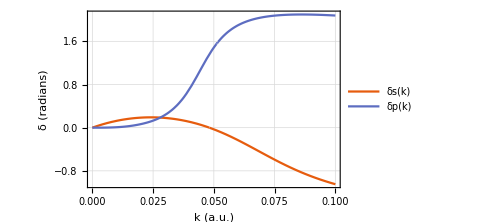

```mathematica
Plot[{δs[k],δp[k]},{k,0,0.1}, FrameLabel->{"k (a.u.)", "δ (radians)"}]
```

#### Semi-classical potentials

```mathematica
Es = Table[With[{δ=δs[Re[kin[r,n0]]]},1/(2n0^2)-1/(2(n0-δ/π)^2)],{r,R}];
Ep = Table[With[{δ=δp[Re[kin[r,n0]]]},1/(2n0^2)-1/(2(n0-δ/π)^2)],{r,R}];
```

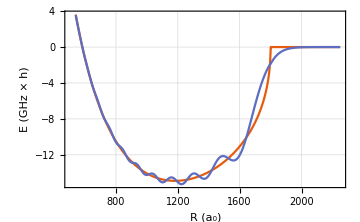

```mathematica
ListLinePlot[{{R,Es unit}ᵀ,{R,dt unit}ᵀ}]
```

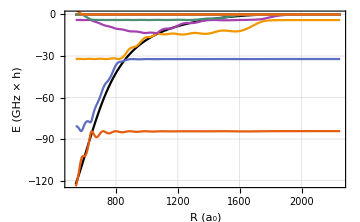

```mathematica
Show[ListLinePlot[{R,Ep unit}ᵀ, PlotStyle->Black], ListLinePlot[pesP0ᵀ,DataRange->{R[[1]],R[[-1]]}]]
```

## Vibrational structure

### s - state potential

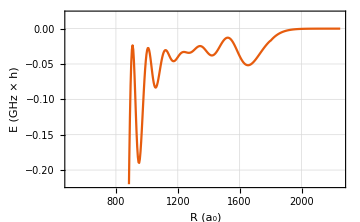

```mathematica
pesTMP = pesP0[[All,32]] - pesP0[[-1,32]];
ListLinePlot[{{R,pesTMP}ᵀ}, PlotRange->{-0.22,0.02}]
```

### Finite differences Hamiltonian and diagonalization

```mathematica
TridiagMat[n_,{ons_,hop_}]:=SparseArray[{Band[{1,1}]->ons,Band[{2,1}]->hop,Band[{1,2}]->hop},{n,n}]
RadSol[pot_, boundary_, gridpoints_, offset_, nstates_] := (
potINT=Interpolation[{R,pot/unit}ᵀ];
Rspan=Subdivide[R[[1]]+boundary,R[[-1]],gridpoints-1];
gridstep=N[(R[[-1]]-R[[1]]-boundary)/(gridpoints-1)];
hop=-1/(M gridstep^2);
ons=-2hop;
Ekin=TridiagMat[gridpoints,{ons,hop}];
shift=-5000IdentityMatrix[gridpoints];
H=shift+Ekin+DiagonalMatrix[potINT[Rspan]];
EigSys=Eigensystem[H,-nstates, Method->{"Arnoldi", "Shift"->offset/unit-5000}];
Vals=(Sort[EigSys[[1]]]+5000) unit;
Vecs=EigSys[[2]][[Ordering[EigSys[[1]]]]];
{Vals, Vecs, Rspan})
```

### The vibrational states depend on the number of grid points except for the well localized parts

#### 401 gridpoints

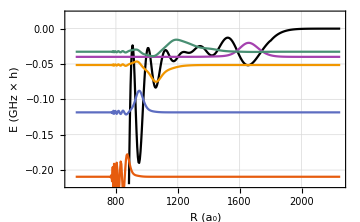

```mathematica
Vib = RadSol[pesTMP,0,401,-0.2,10];
Show[ListLinePlot[{{R,pesTMP}ᵀ}, PlotRange->{-0.22,0.02}, PlotStyle->Black],
ListLinePlot[Evaluate@Table[{Vib[[3]],Vib[[1,i]]+Vib[[2,i]]/10}ᵀ, {i,5}]]]
```

#### 1001 gridpoints

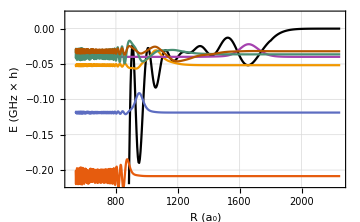

```mathematica
Vib = RadSol[pesTMP,0,1001,-0.2,10];
Show[ListLinePlot[{{R,pesTMP}ᵀ}, PlotRange->{-0.22,0.02}, PlotStyle->Black],
ListLinePlot[Evaluate@Table[{Vib[[3]],Vib[[1,i]]-Vib[[2,i]]/7}ᵀ, {i,6}]]]
```

### Vibrational energies varying the inner boundary

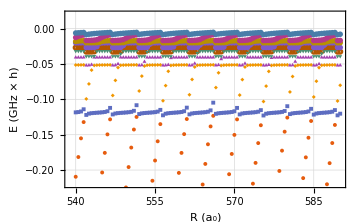

```mathematica
VibStat = Table[With[{Vib=RadSol[pesTMP,i,401,-0.2,10]}, Vib[[1]]],{i,0,50,0.5}];
ListPlot[VibStatᵀ,PlotRange->{-0.22,0.02},DataRange->{R[[1]],R[[1]]+50}, PlotMarkers->{Automatic,Tiny}]
```

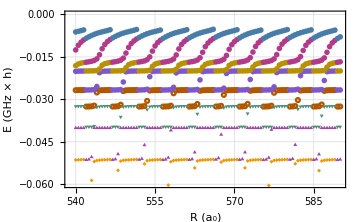

```mathematica
ListPlot[VibStatᵀ,PlotRange->{-0.06,0},DataRange->{R[[1]],R[[1]]+50}, PlotMarkers->{Automatic,Tiny}]
```

### Statistical analysis of the vibrational energies

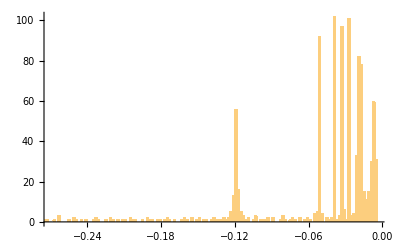

```mathematica
Histogram[Flatten[VibStat],200]
```